```mathematica
Exit
```

## Initialization

Run this section to import the MIRI SIAF

### Import SIAF

```mathematica
siafLocation=FileNameJoin[{NotebookDirectory[],"MIRI_SIAF.xml"}];
```

```mathematica
miriSiafXML=Import[siafLocation];
siafEntriesPre=Cases[miriSiafXML,XMLElement["SiafEntry",_,x_]->x,Infinity];
siafEntriesPre2=Flatten[Cases[#,XMLElement[x_,_,{y_}]->{x->y},{1}]]&/@siafEntriesPre;
instrums="InstrName"/.siafEntriesPre2;
apNames="AperName"/.siafEntriesPre2;
siafEntriesPre3=Table[apNames[[k]]-> Complement[siafEntriesPre2[[k]],{"InstrName"->instrums[[k]],"AperName"->apNames[[k]]}],{k,Length@siafEntriesPre2}];
```

```mathematica
ilumImDir=FileNameJoin[{NotebookDirectory[],"f1065c.fits"}];
```

```mathematica
ilumIm=First@Import[ilumImDir,"RawData"];
pic2=ArrayPlot[ilumIm,DataReversed->True]
```

### Import flat files for reference

```mathematica
Clear@MakeAperture
MakeAperture=Compile[{R1,m,n},Module[{i,j,n0},n0=n/2+1;
N[Table[If[Sqrt[(i-n0)^2+(j-n0)^2]<R1,1,0],{i,m},{j,n}]]]];
```

```mathematica
submat[mat_,p1_,p2_]:=mat[[p1[[2]];;p2[[2]],p1[[1]];;p2[[1]]]]
```

```mathematica
apers={"MIRIM_MASK1065","MIRIM_MASK1550","MIRIM_MASK1140","MIRIM_MASKLYOT"};
keysofInterest={"XSciSize","YSciSize"};
keysLocation={"XDetRef","YDetRef","XSciRef","YSciRef"};
tmpMaskDir=NotebookDirectory[]<>"psf_masks_old/";
psf1065mask=Import[tmpMaskDir<>"jwst_miri_psfmask_0001.fits","RawData"][[2]];
psf1550mask=Import[tmpMaskDir<>"jwst_miri_psfmask_0002.fits","RawData"][[2]];
psf1140mask=Import[tmpMaskDir<>"jwst_miri_psfmask_0003.fits","RawData"][[2]];
psfLYOTmask=Import[tmpMaskDir<>"jwst_miri_psfmask_0004.fits","RawData"][[2]];
refs={psf1065mask,psf1550mask,psf1140mask,psfLYOTmask};
```

```mathematica
(*this block of code cuts out the coronagraphic subarrays from the backlit image of the MIRI FULL array - this can be used to check the mask files*)
illumIms=Table[
aperName=apers[[k]];
siafEntry=aperName/.siafEntriesPre3;
{xdims,ydims}=Map[ToExpression,keysofInterest/.siafEntry];
{xDetRef,yDetRef,xSciRef,ySciRef}=ToExpression/@(keysLocation/.siafEntry);
firstPix=Round[{xDetRef-xSciRef+1,yDetRef-ySciRef+1}];
point2=(firstPix+{xdims,ydims})-1;
submat[ilumIm,firstPix,point2]
,{k,Length@apers}];
```

```mathematica
Print[pic2];
```

```mathematica
fileDir=NotebookDirectory[]<>"flat_files/";
flatData=Import[fileDir<>#,"RawData"]&/@{"jwst_miri_flat_0413.fits","jwst_miri_flat_0424.fits","jwst_miri_flat_0457.fits","jwst_miri_flat_0407.fits"};
```

```mathematica
(*defining the apertures and their IWAs*)
apers={"MIRIM_MASK1065","MIRIM_MASK1550","MIRIM_MASK1140","MIRIM_MASKLYOT"};
IWAS={0.33,0.49,0.36,2.16};
pixelScale=0.11;
kass=Association@Thread[apers->Range@Length@apers];
```

center 1065 = 121, 115

## LYOT

```mathematica
k=4;
```

```mathematica
Row@{ArrayPlot[illumIms[[k]],DataReversed->True,PlotLabel->Style["Backlit LYOT Subarray",18],ImageSize->400],ArrayPlot[refs[[k]],DataReversed->True,PlotLabel->Style["LYOT PSFMASK Reference File",18],ImageSize->400],ArrayPlot[refs[[k]]*illumIms[[k]],DataReversed->True,PlotLabel->Style["Overlay of PSFMASK and Backlit Subarray",18],ImageSize->400]}
```

```mathematica
lyotFlat=flatData[[k]];
```

```mathematica
Last@lyotFlat//MatrixForm
```

```mathematica
ArrayPlot[lyotFlat[[2]],DataReversed->True]
ArrayPlot[lyotFlat[[3]],DataReversed->True]
ArrayPlot[lyotFlat[[4]],DataReversed->True]
(*ArrayPlot[finres,DataReversed->True]*)
```

```mathematica
res2=(lyotFlat[[3]]/.Indeterminate->0)/.∞->0;
Max@res2
```

```mathematica
repNum=999999999999999999999999999;
res2=(lyotFlat[[3]]/.Indeterminate->repNum)/.∞->repNum;
Min@res2
```

```mathematica
dqvals=DeleteDuplicates@Flatten@lyotFlat[[4]]
```

```mathematica
res3=lyotFlat[[4]]/.{Max@dqvals->0,Min@dqvals->1};
```

```mathematica
ArrayPlot[res3,DataReversed->True]
res4=Floor@MedianFilter[res3,1];
ArrayPlot[res4,DataReversed->True]
```

```mathematica
dims=res4//Dimensions
res = 1-MakeAperture[20,dims[[1]],dims[[2]]];
%//Dimensions
ArrayPlot[res]
```

```mathematica
x1=10;
x2=30;
y1=20;
y2=40;
```

```mathematica
(*This Manipulate function is used to move the mask around to match the correspionding flat file*)
moveMax=100;
Manipulate[
res =1- MakeAperture[r,dims[[1]],dims[[2]]];
finres=Transpose[RotateLeft[Transpose[RotateLeft[res,posX]],posY]];

finres[[1;;x1]]=ConstantArray[0,{x1,dims[[2]]}];
finres[[-x2;;-1]]=ConstantArray[0,{x2,dims[[2]]}];
finres[[1;;,1;;y1]]=ConstantArray[0,{dims[[1]],y1}];
finres[[1;;,-y2;;-1]]=ConstantArray[0,{dims[[1]],y2}];
(*finres[[168,145]]=1;*)

figs={finres,res4,finres*res4};

ArrayPlot[figs[[fignum]],DataReversed->True],{{r,20},1,50,1},{{posX,-6},-50,50,1},{{posY,16},-50,50,1},{{fignum,1},1,3,1},
{{x1,34},1,moveMax,1},{{x2,2},1,moveMax,1},{{y1,9},1,moveMax,1},{{y2,42},1,moveMax,1}]
```

```mathematica
res4=res3;
res4[[168,145]]=1;
ArrayPlot[res4,DataReversed->True]
```

```mathematica
(*here I export the new mask file*)
expdir=expDirPre<>"jwst_miri_psfmask_000"<>ToString@k<>"_npre.fits";
Export[expdir,finres];
```

## MASK1065

```mathematica
apers[[1]]
```

```mathematica
k=kass["MIRIM_MASK1065"];
Print[apers[[k]]];
Print[ArrayPlot[illumIms[[k]],DataReversed->True]];
Print[ArrayPlot[refs[[k]],DataReversed->True]];
res=refs[[k]];
zeros=Position[res,0.0];
ones=Position[res,1.0];
```

```mathematica
flat=flatData[[k]];
res3=flat[[4]]/.{-2147483582->0,-2147483648->1};
DeleteDuplicates@Flatten@res3
IWA= IWAS[[k]];
initR=Ceiling[IWA/pixelScale]

ArrayPlot[flat[[2]],DataReversed->True]
ArrayPlot[flat[[3]],DataReversed->True]
ArrayPlot[finres,DataReversed->True]
ArrayPlot[res3,DataReversed->True,PlotLabel->"res3"]
```

```mathematica
dims=Dimensions@res3;
Manipulate[
res = 1-MakeAperture[r,dims[[1]],dims[[2]]];
finres=Transpose[RotateLeft[Transpose[RotateLeft[res,posX]],posY]];
(*finres[[168,145]]=1;*)
(*finfinres=finres*res3;*)
finfinres4real=finres*Floor@MedianFilter[res3,1];

finfinres4real[[1;;x1]]=ConstantArray[0,{x1,dims[[2]]}];
finfinres4real[[-x2;;-1]]=ConstantArray[0,{x2,dims[[2]]}];
finfinres4real[[1;;,1;;y1]]=ConstantArray[0,{dims[[1]],y1}];
finfinres4real[[1;;,-y2;;-1]]=ConstantArray[0,{dims[[1]],y2}];


figs={finres,res3,finfinres,finfinres4real};

ArrayPlot[figs[[fignum]],DataReversed->True],{{r,initR},1,50,1},{{posX,31},-50,50,1},{{posY,23},-50,50,1},{{fignum,4},1,4,1},
{{x1,7},1,moveMax,1},{{x2,4},1,moveMax,1},{{y1,14},1,moveMax,1},{{y2,60},1,moveMax,1}]
```

```mathematica
ArrayPlot[finfinres4real,DataReversed->True]
```

```mathematica
expdir=expDirPre<>"jwst_miri_psfmask_000"<>ToString@k<>"_npre.fits";
Export[expdir,finfinres4real]
```

```mathematica
(*{{posX,-2},-50,50,1},{{posY,23},-50,50,1},{{n,1},0,10,1}*)
```

## MASK1550

```mathematica
apers[[2]]
```

MIRIM_MASK1550

-Graphics-

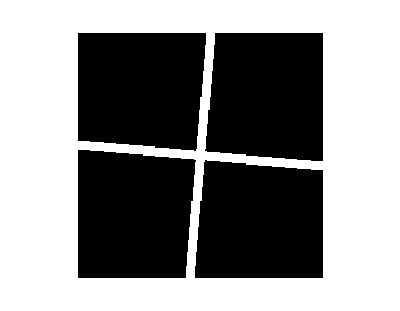

```mathematica
k=kass["MIRIM_MASK1550"];
Print[apers[[k]]];
Print[ArrayPlot[illumIms[[k]],DataReversed->True]];
Print[ArrayPlot[refs[[k]],DataReversed->True]];
res=refs[[k]];
zeros=Position[res,0.0];
ones=Position[res,1.0];
```

{0,1}

5

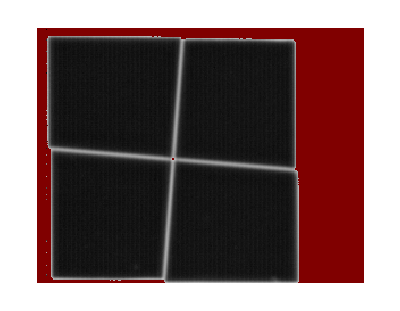

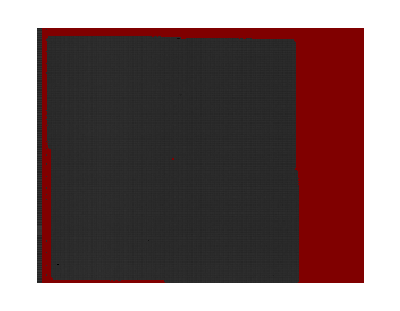

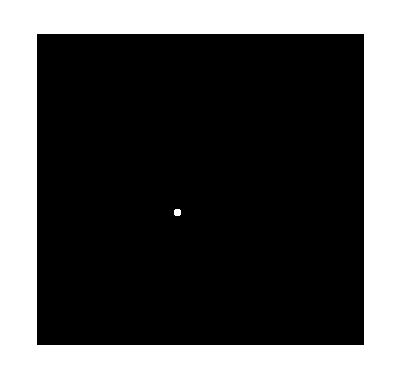

-Graphics-

```mathematica
flat=flatData[[k]];
res3=flat[[4]]/.{-2147483582->0,-2147483648->1};
DeleteDuplicates@Flatten@res3
IWA= IWAS[[k]];
initR=Ceiling[IWA/pixelScale]

ArrayPlot[flat[[2]],DataReversed->True]
ArrayPlot[flat[[3]],DataReversed->True]
ArrayPlot[finres,DataReversed->True]
ArrayPlot[res3,DataReversed->True,PlotLabel->"res3"]
```

```mathematica
dims=Dimensions@res3;
Manipulate[
res = 1-MakeAperture[r,dims[[1]],dims[[2]]];
finres=Transpose[RotateLeft[Transpose[RotateLeft[res,posX]],posY]];
finfinres4real=finres*Floor@MedianFilter[res3,1];
finfinres4real[[1;;x1]]=ConstantArray[0,{x1,dims[[2]]}];
finfinres4real[[-x2;;-1]]=ConstantArray[0,{x2,dims[[2]]}];
finfinres4real[[1;;,1;;y1]]=ConstantArray[0,{dims[[1]],y1}];
finfinres4real[[1;;,-y2;;-1]]=ConstantArray[0,{dims[[1]],y2}];
figs={finres,res3,finfinres4real};

ArrayPlot[figs[[fignum]],DataReversed->True],{{r,initR},1,50,1},{{posX,35},-50,50,1},{{posY,24},-50,50,1},{{fignum,3},1,3,1},
{{x1,4},1,moveMax,1},{{x2,12},1,moveMax,1},{{y1,13},1,moveMax,1},{{y2,61},1,moveMax,1}]
```

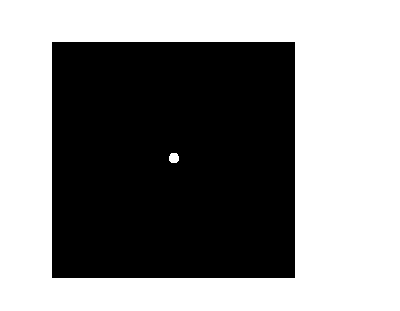

```mathematica
ArrayPlot[finfinres4real,DataReversed->True]
```

```mathematica
Manipulate[ListLinePlot[finfinres4real[[k]]],{{k,114},1,320,1}]
```

```mathematica
expdir=expDirPre<>"jwst_miri_psfmask_000"<>ToString@k<>"_npre.fits";
Export[expdir,finfinres4real]
```

```mathematica
(*{{posX,-2},-50,50,1},{{posY,23},-50,50,1},{{n,1},0,10,1}*)
```

## MASK1140

```mathematica
apers[[3]]
```

MIRIM_MASK1140

```mathematica
k=kass["MIRIM_MASK1140"];
Print[apers[[k]]];
Print[ArrayPlot[illumIms[[k]],DataReversed->True]];
Print[ArrayPlot[refs[[k]],DataReversed->True]];
res=refs[[k]];
zeros=Position[res,0.0];
ones=Position[res,1.0];
```

MIRIM_MASK1140

-Graphics-

-Graphics-

{0,1}

4

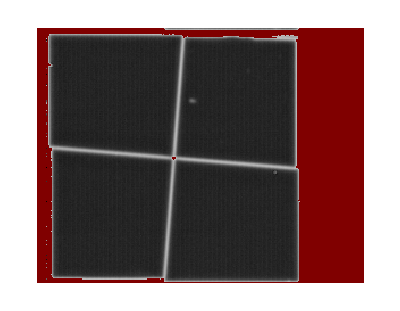

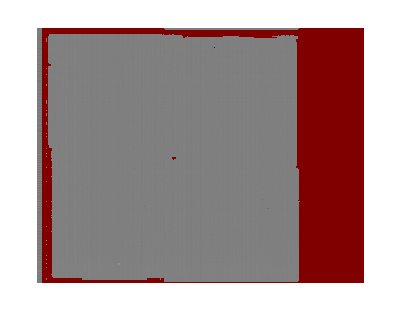

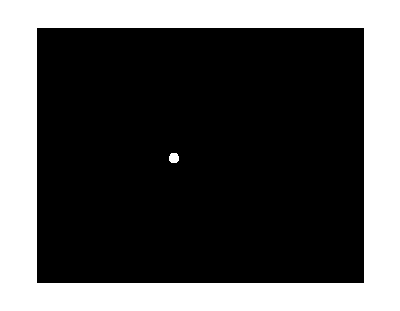

-Graphics-

```mathematica
flat=flatData[[k]];
res3=flat[[4]]/.{-2147483582->0,-2147483648->1};
DeleteDuplicates@Flatten@res3
IWA= IWAS[[k]];
initR=Ceiling[IWA/pixelScale]

ArrayPlot[flat[[2]],DataReversed->True]
ArrayPlot[flat[[3]],DataReversed->True]
ArrayPlot[finres,DataReversed->True]
ArrayPlot[res3,DataReversed->True,PlotLabel->"res3"]
```

```mathematica
dims=Dimensions@res3;
Manipulate[
res = 1-MakeAperture[r,dims[[1]],dims[[2]]];
finres=Transpose[RotateLeft[Transpose[RotateLeft[res,posX]],posY]];
finfinres4real=finres*Floor@MedianFilter[res3,1];
finfinres4real[[1;;x1]]=ConstantArray[0,{x1,dims[[2]]}];
finfinres4real[[-x2;;-1]]=ConstantArray[0,{x2,dims[[2]]}];
finfinres4real[[1;;,1;;y1]]=ConstantArray[0,{dims[[1]],y1}];
finfinres4real[[1;;,-y2;;-1]]=ConstantArray[0,{dims[[1]],y2}];
figs={finres,res3,finfinres,finfinres4real};

ArrayPlot[figs[[fignum]],DataReversed->True],{{r,initR},1,50,1},{{posX,34},-50,50,1},{{posY,24},-50,50,1},{{fignum,4},1,4,1},
{{x1,5},1,moveMax,1},{{x2,9},1,moveMax,1},{{y1,13},1,moveMax,1},{{y2,60},1,moveMax,1}]
```

```mathematica
ArrayPlot[finfinres4real,DataReversed->True]
```

```mathematica
expdir=expDirPre<>"jwst_miri_psfmask_000"<>ToString@k<>"_npre.fits";
Export[expdir,finres]
```